```mathematica
f[x_]=x^3-4x+2
```

2-4 x+x^3

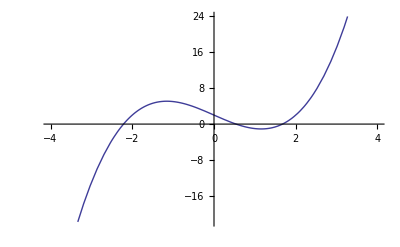

```mathematica
Plot[f[x],{x,-4,4}]
```

```mathematica
FindRoot[f[x],{x,0}]
```

{x→0.539189}

```mathematica
FindRoot[f[x],{x,2}]
```

{x→1.67513}

```mathematica
ClearAll[newton]
```

```mathematica
SetAttributes[newton,HoldAll]
```

```mathematica
newton[f_[x_], {x_, x0_}]:=Module[ {d, fx,dx, xp},
d = D[f[x],x];
fx = 1;
dx=x0;
xp = 0;
While[Abs[fx] > 1*^-4,
fx = Evaluate[f[dx]];
xp = dx;
dx  = dx - fx/Evaluate[d/.x->dx]
];
N[xp]
]
```

```mathematica
newton[f[x],{x,0}]
```

0.539189